```mathematica
SetDirectory["/home/lina/Documents/SimulacionesTesis/resultados3/v2/data"];
```

```mathematica
(*data1=Map[Partition[#,30]&,ToExpression@Import["OneGenR_0.6","CSV"]][[All,All,1;;25]];*)
```

```mathematica
(*Export["OneGenR_0.5",Map[Partition[Flatten[#,2],2]&,data1],"CSV"]*)
```

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4"]
```

/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4/csv"]
```

/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4/csv

```mathematica
SetDirectory["/home/lina/Documents"]
```

/home/lina/Documents

## Graficas individuales

## control Munsky

### Escalas características

```mathematica
data=ToExpression@Table[Import["control_Munsky_γg"<>i,"CSV"],{i,{"20","40","60","80","100"}}];
```

```mathematica
data[[1;;2]]
```

{{{1.1966,0.011791},{0.509772,0.999565},{0.509772,0.999565},{0.508535,0.999753},{0.504102,1.00021},{0.509155,0.999662},{0.509155,0.999662},{0.508535,0.999753},{0.510994,0.999352},{0.5134,0.998851},49981,{84.7112,0.0530268},{91.2752,0.057931},{91.9485,0.0575766},{86.1686,0.0552306},{85.6402,0.0551741},{85.5226,0.0542374},{92.7601,0.0599878},{91.1268,0.0591735},{87.5137,0.0560913}},{1}}
 |  |  |  |

```mathematica
(****************************************************)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,100]&,data[[All,All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,100]&,data[[All,All,2(*cv2*)]]]]];
```

```mathematica
(****************************************************)
modelo="control_Munsky ";
```

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.01,100},{0.01,100}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium,ScalingFunctions->{"Log","Log"}],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA"}}}]
```

{-Graphics-,-Graphics-}

## GA

### Escalas características

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4/csv_porOrdenar1"]
```

/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4/csv_porOrdenar1

```mathematica
(**********************************)
```

```mathematica
data=ToExpression@Table[Import["controlUnRGA_γg"<>i<>".csv"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlRGA_γg"<>i<>"2"],{i,{"0.5","1.","1.5.","2."}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AI2γg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_II2γg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_AIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_IIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAI_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
(******************************************+)
```

```mathematica
data=ToExpression@ImportString[#,"CSV"]&/@data;
```

ImportString::string: First argument {{5.130868339632227, 0.030576301288972742, 6819752100336479882/39317994149906175}","{5.988978492855897, 0.05860090138233402, 62027909245983505318196982261067762924160147/530996012619119368169709446383932141621600}","{3.6094182116218634, 0.04312378568089…{3.817439046929542, 0.2309887856766875, 5025735753624129678756081275833827222470803/290386494963161874977645119639861390075200}","{4.635051991517199, 0.29292668512955145, 15813878361998859462541801093223888277809/971756210846650734559489307039180496000}} is not a string.

ToExpression::notstrbox: ImportString[{{5.130868339632227, 0.030576301288972742, 6819752100336479882/39317994149906175}","{5.988978492855897, 0.05860090138233402, 62027909245983505318196982261067762924160147/530996012619119368169709446383932141621600}","{3.6094182116218634, 0.043123…046929542, 0.2309887856766875, 5025735753624129678756081275833827222470803/290386494963161874977645119639861390075200}","{4.635051991517199, 0.29292668512955145, 15813878361998859462541801093223888277809/971756210846650734559489307039180496000}},CSV] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ImportString::string: First argument {{323.23609097027224, 0.030372569125692805, 1741503427936768240589/157271976599624700}","{309.51300312694354, 0.043632444225906064, 16852612015057125257441696613988115287423509/2240489504722022650505103149299291736800}","{187.24109255295687, 0.033062265…4992593840492, 0.13158077559128256, 39092443631734338559125462045579613531465601/36298311870395234372205639954982673759400}","{182.19898641003357, 0.18327666292580758, 2973370049618637148912069110648533824158767/2915268632539952203678467921117541488000}} is not a string.

ToExpression::notstrbox: ImportString[{{323.23609097027224, 0.030372569125692805, 1741503427936768240589/157271976599624700}","{309.51300312694354, 0.043632444225906064, 16852612015057125257441696613988115287423509/2240489504722022650505103149299291736800}","{187.24109255295687, 0.0…0492, 0.13158077559128256, 39092443631734338559125462045579613531465601/36298311870395234372205639954982673759400}","{182.19898641003357, 0.18327666292580758, 2973370049618637148912069110648533824158767/2915268632539952203678467921117541488000}},CSV] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

```mathematica
data=Table[Import["controlRGAγm"<>i],{i,{"0.025","0.05","0.075","0.1"}}][[1]];
```

```mathematica
data=Table[Import["controlRGA_γg"<>i<>"2"],{i,{"0.5","1.","1.5.","2."}}];
```

```mathematica
data=ToExpression@Table[Import["controlRGA_γg"<>i<>".csv"],{i,{"0.42","0.92","1.42","1.92"}}];
```

Import::nffil: File controlRGA_γg0.42.csv not found during Import.

Import::nffil: File controlRGA_γg0.92.csv not found during Import.

Import::nffil: File controlRGA_γg1.42.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
data=ToExpression@Table[Import["kγg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["controlUnRGA_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["controlRGA_γg"<>i<>"0.01158","CSV"],{i,{"0.5","1.","1.5","2"}}];
```

Import::nffil: File \"\<controlRGA_γg0.50.01158\>\" not found during Import.

Import::nffil: File controlRGA_γg1.0.01158 not found during Import.

Import::nffil: File controlRGA_γg1.50.01158 not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
data=ToExpression@Table[Import["controlRGA_γp"<>i<>".csv","CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

Import::nffil: File controlRGA_γp0.025.csv not found during Import.

Import::nffil: File controlRGA_γp0.05.csv not found during Import.

Import::nffil: File controlRGA_γp0.075.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
data1=ToExpression@Table[Import["controlRGA_γg"<>i<>".csv","CSV"],{i,{"0.5","1.","1.5","2"}}];
```

Part::partw: Part 1 of {} does not exist.

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

```mathematica
Position[NumberQ/@(data1[[#]]//Flatten),False]&/@{1,2,3,4}
```

{{},{{4885},{4886},{4887},{7096},{7097},{7098},{12385},{12386},{12387},{14596},{14597},{14598}},{},{{3130},{3131},{3132},{3385},{3386},{3387},{6715},{6716},{6717},{10630},{10631},{10632},{10885},{10886},{10887},{14215},{14216},{14217}}}

```mathematica
data=Replace[data1//N,x_/;NumberQ[x]==False->0,{4}];
```

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+955 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+787 (-1+{}⟦1,1⟧);;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

```mathematica
Range[0.02,2,0.1]//Partition[#,5]&
```

{{0.02,0.12,0.22,0.32,0.42},{0.52,0.62,0.72,0.82,0.92},{1.02,1.12,1.22,1.32,1.42},{1.52,1.62,1.72,1.82,1.92}}

```mathematica
Range[0.02,2,0.02]//Partition[#,25]&
```

{{0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5},{0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.},{1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5},{1.52,1.54,1.56,1.58,1.6,1.62,1.64,1.66,1.68,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98,2.}}

```mathematica
(****************************************************)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
(******************************************2000 pts**********)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
(****************************************************)
modelo="controlGA I-A ΔI para I";
```

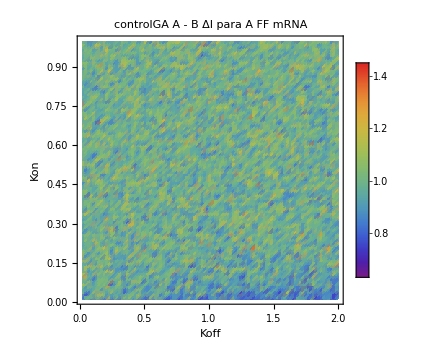
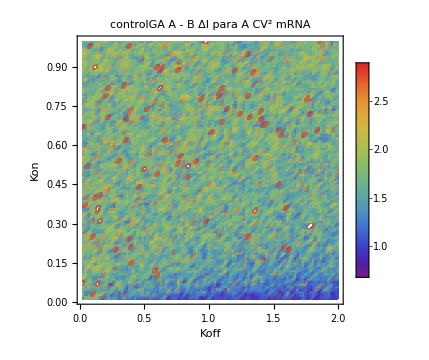
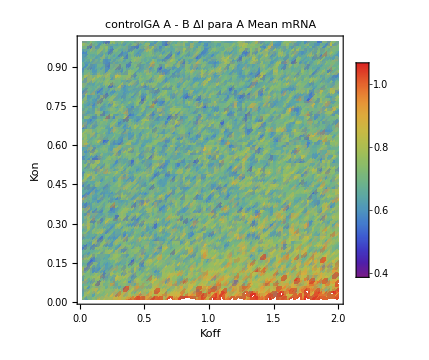
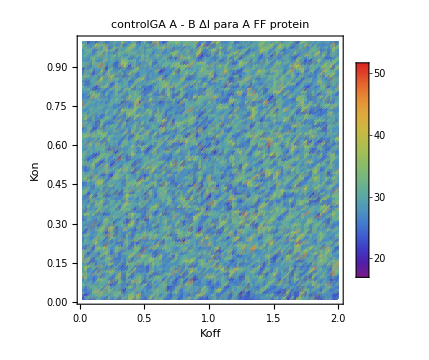
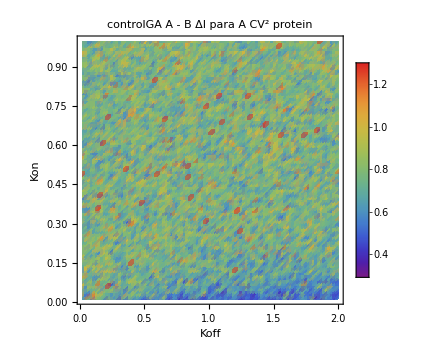
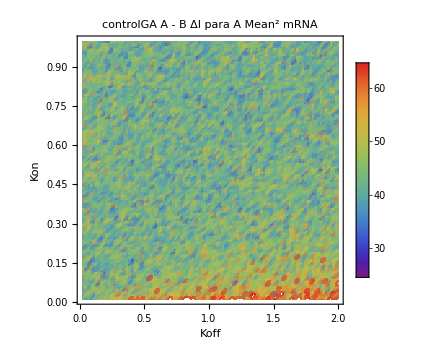

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA"},{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA"},{meanmRNA,ToString[modelo]<>" \n  Mean mRNA"},{ffProtein,ToString[modelo]<>" \n  FF protein"},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein"},{meanProtein,ToString[modelo]<>" \n  Mean^2 mRNA"}}}]
```

```mathematica
(***Para los que no cambian***)
```

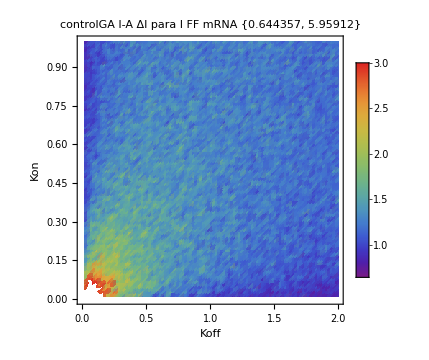
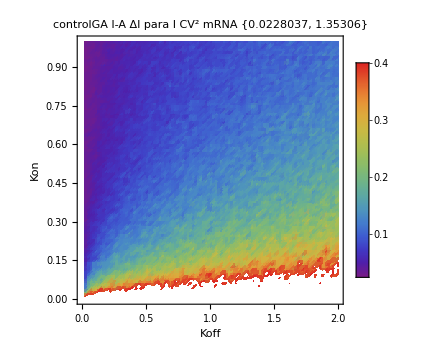
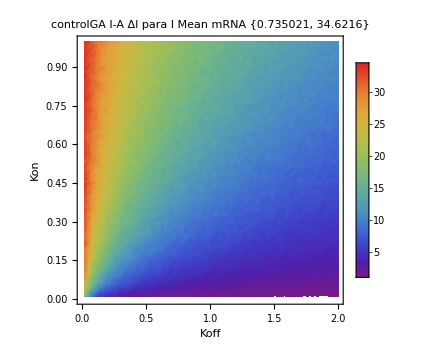
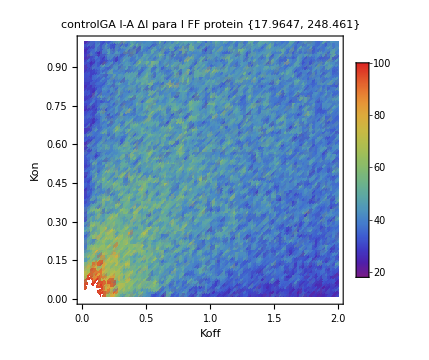
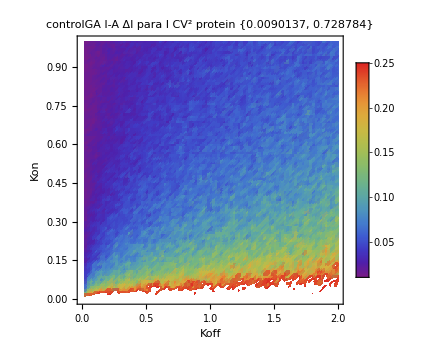
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},i[[3]],ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA//N],PlotRange-> {0.45,3}},
{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA "<>ToString[MinMax@Flatten@cv2mRNA//N],PlotRange->{0.02,0.4}},
{meanmRNA,ToString[modelo]<>" \n  Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA//N],PlotRange->{1,35}},{ffProtein,ToString[modelo]<>" \n  FF protein "<>ToString[MinMax@Flatten@ffProtein//N],PlotRange-> {15,100}},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein "<>ToString[MinMax@Flatten@cv2Protein//N],PlotRange->{0.01,0.25}},{meanProtein,ToString[modelo]<>" \n  Mean^2 mRNA "<>ToString[MinMax@Flatten@meanProtein//N],PlotRange->{50,2300}}}}]
```

```mathematica
ffmRNA[[1,1]]=0.45;ffmRNA[[1,2]]=3;
cv2mRNA[[1,1]]=0.6;cv2mRNA[[1,2]]=4;
meanmRNA[[1,1]]=0.3;meanmRNA[[1,2]]=1.2;
ffProtein[[1,1]]=15;ffProtein[[1,2]]=100;
cv2Protein[[1,1]]=0.3;cv2Protein[[1,2]]=1.65;
meanProtein[[1,1]]=10;meanProtein[[1,2]]=76;
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},i[[3]],ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA//N],PlotRange-> {0.45,3}},
{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA "<>ToString[Mean@Flatten@cv2mRNA//N],PlotRange->{0.6,4}},
{meanmRNA,ToString[modelo]<>" \n  Mean mRNA "<>ToString[Mean@Flatten@meanmRNA//N],PlotRange->{0.3,1.2}},{ffProtein,ToString[modelo]<>" \n  FF protein "<>ToString[Mean@Flatten@ffProtein//N],PlotRange-> {15,100}},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein "<>ToString[Mean@Flatten@cv2Protein//N],PlotRange->{0.3,1.65}},{meanProtein,ToString[modelo]<>" \n  Mean^2 mRNA "<>ToString[Mean@Flatten@meanProtein//N],PlotRange->{10,76}}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## burstmRNA

```mathematica
data=ToExpression@Table[Import["burstmRCLE_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmRCLE_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEInh_I_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEInh_I_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEAct_I_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2."}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEAct_A_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
(****************************************************)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
(****************************************************)
```

```mathematica
modelo="burstmRNA, One G R CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_A_A, CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_A_I, CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_I_A, CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_I_I, CLE";
```

```mathematica
modelo="Act-Inh_A_, GA";
```

```mathematica
modelo="Act-Inh_I_I, GA";
```

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA"},{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA"},{ffProtein,ToString[modelo]<>" \n  FF protein"},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein"}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## bothBurst

```mathematica
(*{"0.025","0.05","0.075","0.1"}{"0.5","1.","1.5","2"} *)
```

```mathematica
data2=ToExpression@Table[Import["bothBRCLE2γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1,All,1]][[All,All,1]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1,All,1]][[All,All,2]]]]];
```

```mathematica
(*OneGen*)
modelo="CLE";Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->(*{"Koff","Kon"}*){"KdmRNA","Koff"}(*{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.02,2}(*{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein,"BothB One Gen R "<>ToString[modelo]<>" \n  FF protein"},{cv2Protein,"BothB One Gen R "<>ToString[modelo]<>" \n  CV^2 protein"}}}]
```

## burstProtein

```mathematica
data=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γg"<>i,"CSV"],{i,{"1.5","2"}}]];
```

```mathematica
data=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}]];
```

```mathematica
(****************************************************)
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,All,2(*cv2*)]]]]];
```

```mathematica
(****************************************************)
```

```mathematica
modelo="burstP, One G R CLE";
```

```mathematica
modelo="burstP, Act-Inh_A_A, CLE";
```

```mathematica
modelo="burstP, Act-Inh_A_I, CLE";
```

```mathematica
modelo="burstP, Act-Inh_I_A, CLE";
```

```mathematica
modelo="burstP, Act-Inh_I_I, CLE";
```

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein,ToString[modelo]<>" \n  FF protein"},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein"}}}]
```

{-Graphics-,-Graphics-}

## Comparando

## Procesando datos

### Funciones

```mathematica
JSDDivergence[data1_,data2_,delta_,quantile_List]:=Module[{data1cut,data2cut,range,pList,qList,mList,divergence},
data1cut=Select[Flatten[data1],Quantile[Flatten[data1],quantile][[1]]<#<Quantile[Flatten[data1],quantile][[2]]&];
data2cut=Select[Flatten[data2],Quantile[Flatten[data2],quantile][[1]]<#<Quantile[Flatten[data2],quantile][[2]]&];
range={Min[Flatten[{data1cut,data2cut}]],Max[Flatten[{data1cut,data2cut}]]};
{pList,qList}=Transpose@Table[{PDF[HistogramDistribution[data1cut],x],PDF[HistogramDistribution[data2cut],x]},{x,Range[Sequence@@range,delta]}];
mList=(pList+qList)/2;
divergence=1/2 Total@DeleteCases[Table[pList[[i]]*Log[pList[[i]]/(mList[[i]]+0.000001)],{i,1,Length[pList]}],Indeterminate]+1/2 Total@DeleteCases[Table[qList[[i]]*Log[qList[[i]]/(mList[[i]]+0.000001)],{i,1,Length[qList]}],Indeterminate]](* Cuando aparecen errores de indeterminación es porque las curvas no se solapan en ningun punto*)
```

```mathematica
histograma[label_,plotlabel_,color_,data_List,quantile_List]:=Histogram[Select[Flatten[data],Quantile[Flatten[data],quantile][[1]]<#<Quantile[Flatten[data],quantile][[2]]&],"Sturges","Probability",Frame->True,FrameLabel->label,PlotLabel-> plotlabel,ImageSize-> Small,ChartStyle->color]
```

```mathematica
ttest[data_List]:=Table[TTest[{data[[i]],data[[j]]},0,"PValue"],{i,Length[data]},{j,Length[data]}]//MatrixForm
```

```mathematica
MWtest[data_List,quantile_List]:=Module[{data2},
data2=Table[Select[Flatten[i],Quantile[Flatten[i],quantile][[1]]<#<Quantile[Flatten[i],quantile][[2]]&],{i,data}];Table[MannWhitneyTest[{data2[[i]],data2[[j]]},0,"PValue"],{i,Length[data2]},{j,Length[data2]}]//MatrixForm]
```

## Comparando metodologia con OneGenR -histogramas

### Cargando datos

```mathematica
data1=ToExpression@Table[Import["controlRGA_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data2=ToExpression@Table[Import["burstmRCLE_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data3=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}]];
data4=ToExpression@Table[Import["bothBRCLE_γg"<>i,"CSV"],{i,{"0.5","1","1.5","2"}}];
```

```mathematica
data1=ToExpression@Table[Import["controlRGA_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data2=ToExpression@Table[Import["burstmRCLE_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data3=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}]];
data4=ToExpression@Table[Import["bothBRCLE_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
(****************************************************)
```

```mathematica
ffmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,All,1(*FF*)]]]]];
cv2Protein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,All,2(*cv2*)]]]]];
```

```mathematica
ffProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1,All,1]][[All,All,1]]]]];
cv2Protein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1,All,1]][[All,All,2]]]]];
```

### Kdp-KdmRNA One Gene Regulated

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

(-8.99967×10^-6 | 2.71663
2.71663 | -0.0000119997)

(-3.×10^-6 | 3.29245
3.29245 | -3.×10^-6)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,CLE","PDF"},Flatten@cv2mRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-9.99999×10^-6 | 4.18384
4.18384 | -0.0000209999)

(-6.99999×10^-6 | 5.35656
5.35656 | -0.000013)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein,bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-9.98752×10^-7 | 0.0000635494 | 0.0263166 | 0.0263519
0.0000635494 | -1.98517×10^-6 | 0.0270557 | 0.0262199
0.0263166 | 0.0270557 | -4.97396×10^-6 | 0.0261083
0.0263519 | 0.0262199 | 0.0261083 | -6.91777×10^-6)

(-0.0000249991 | 0.0714798 | 0.0911332 | 0.256095
0.0714798 | -0.0000249989 | 0.195876 | 0.302495
0.0911332 | 0.195876 | -0.0000669809 | 0.152783
0.256095 | 0.302495 | 0.152783 | -0.000115963)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein,bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-6.99997×10^-6 | 2.23362 | 1.47526 | 6.99644
2.23362 | -0.000049991 | 2.36819 | 6.4485
1.47526 | 2.36819 | -0.0000179989 | 6.78173
6.99644 | 6.4485 | 6.78173 | -0.000307955)

(-5.×10^-6 | 2.06107 | 1.96836 | 6.80867
2.06107 | -0.000016 | 2.87886 | 6.72701
1.96836 | 2.87886 | -4.×10^-6 | 7.12255
6.80867 | 6.72701 | 7.12255 | -0.000209997)

### KdmRNA-Koff One Gene Regulated

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
({{-0.00005699795766267894, 0.4041579589230816}, {0.4041579589230816, -0.00009798947251878121}})
```

(-0.0000199999 | 1.01369
1.01369 | -0.0000239998)

```mathematica
MWtest[{ffmRNA1,ffmRNA2},{0.05,0.95}]
```

(0.999999 | 6.24217×10^-182
6.24268×10^-182 | 0.999999)

```mathematica
({{0.9999990225261791, 3.8448253568456856*^-133}, {3.8450570633497445*^-133, 0.9999990225261791}})
```

```mathematica
({{0.9999990228194018, 4.514939936598919*^-133}, {4.515211873467762*^-133, 0.9999990228194018}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,CLE","PDF"},Flatten@cv2mRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-0.0000229994 | 1.58755
1.58755 | -0.0000139999)

```mathematica
({{-9.999956113135698*^-6, 1.8216721529062845}, {1.8216721529062845, -6.99999685873734*^-6}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein, bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-2.99254×10^-6 | 0.053606 | 0.017001 | 0.00394853
0.053606 | -1.999×10^-6 | 0.0537708 | 0.00382007
0.017001 | 0.0537708 | -0.0000108525 | 0.00360347
0.00394853 | 0.00382007 | 0.00360347 | -0.0000259027)

```mathematica
({{-0.00007197954398908529, 0.2993899188801601, 0.11008199705967009, 0.1939729160386217}, {0.2993899188801601, -0.00007798156726603881, 0.1969109042746248, 0.3566430021371841}, {0.11008199705967009, 0.1969109042746248, -0.00015490894157899326, 0.18946423356439052}, {0.1939729160386217, 0.3566430021371841, 0.18946423356439052, -0.00036854933449073407}})
```

```mathematica
MWtest[{ffProtein1,ffProtein2,ffProtein3,ffProtein4},{0.05,0.95}]
```

(0.999999 | 0. | 6.78519×10^-87 | 0.
0. | 0.999999 | 0. | 0.
6.7848×10^-87 | 0. | 0.999999 | 0.
0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]],"OneGR KmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein, bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-0.0000189996 | 2.79598 | 0.628982 | 6.65374
2.79598 | -9.99958×10^-6 | 3.90708 | 6.41625
0.628982 | 3.90708 | -0.0000209989 | 6.66747
6.65374 | 6.41625 | 6.66747 | -0.000272959)

(-6.99999×10^-6 | 4.0067 | 0.941347 | 7.15371
4.0067 | -4.×10^-6 | 6.04897 | 7.48107
0.941347 | 6.04897 | -6.×10^-6 | 6.84946
7.15371 | 7.48107 | 6.84946 | -0.000196996)

### Koff-Kon One Gene Regulated

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0.05,0.95}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
({{-0.00010999918695432057, 5.838195262606714}, {5.838195262606714, -0.0001599953611507452}})
```

```mathematica
({{-0.00003799584324223993, 3.9452712777162353}, {3.9452712777162353, -0.00008097833252158497}})
```

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Black,i[[2]],{0.05,0.95}],{i,{{{"CV2 mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"CV2 mRNA,burstmCLE","PDF"},Flatten@cv2mRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

```mathematica
({{-0.00005999954788806183, 3.9969560398231003}, {3.9969560398231003, -0.0000599996625615129}})
```

(-8.99994×10^-6 | 1.24134
1.24134 | -7.99991×10^-6)

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein, bothBCLE2CLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,1,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein4}}]//MatrixForm
```

```mathematica
({{-0.00014747957513137745, 0.3335968510642072, 0.6410197340942566}, {0.3335968510642072, -0.00023639786011133416, 0.5873943468970071}, {0.6410197340942566, 0.5873943468970071, -0.0009989445852557038}})
```

```mathematica
({{-0.000579707069194458, 0.4510356825075909, 0.6902528814149005}, {0.4510356825075909, -0.0005296126649052828, 0.6888226983559401}, {0.6902528814149005, 0.6888226983559401, -0.0019442654290775497}})
```

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein, bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein4}}]//MatrixForm
```

(-7.99986×10^-6 | 7.58529 | 8.2274
7.58529 | -4.×10^-6 | 2.34369
8.2274 | 2.34369 | -0.0000509952)

```mathematica
({{-4.999996739017614*^-6, 5.7781767420376, 6.50166012360857}, {5.7781767420376, -2.9999992785846943*^-6, 4.645220940355409}, {6.50166012360857, 4.645220940355409, -0.000013999974987104953}})
```

### Comparando diferentes algoritmos- homogenizacion de escala

```mathematica
(****************************************************)
modelo1="controlGA, One R G ";
modelo2="burstmRNA, One R G ";
modelo3="burstP, One R G ";
modelo4="bothBurst, One R G ";
```

```mathematica
ffmRNA2[[1,1]]=0.1;
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {0.1,1.9},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA1,ToString[modelo1]<>" \n FF mRNA"},{ffmRNA2,ToString[modelo2]<>" \n FF mRNA"}}}]
```

{-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {5,80},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein1,ToString[modelo1]<>" \n FF protein"},{ffProtein2,ToString[modelo2]<>" \n FF protein"}(*,{ffProtein3,ToString[modelo3]<>" \n FF protein"}*),{ffProtein4,ToString[modelo4]<>" \n FF protein"}}}]
```

{-Graphics-,-Graphics-,-Graphics-}

## Comparando diferentes subcircuitos con GA

### Cargando datos

```mathematica
(****NOTA IMPORTANTE!!!!!: Cuando tenga lista todos los de GA se hacen estas graficas con la misma escala para todas y poder comparar entre estas. Por el momento solo voy a revisar las que tengo*)
```

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4/csv"]
```

/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4/csv

```mathematica
data0=ToExpression@Table[Import["controlConstGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];ffmRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
(**********************************)
data1=ToExpression@Table[Import["controlUnRGA_γg"<>i<>".csv"],{i,{"0.5","1.","1.5","2"}}];
data2=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlRGA_γg"<>i<>"2"],{i,{"0.5","1.","1.5.","2."}}];
data3=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data4=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data5=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data6=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data7=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data8=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data9=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data10=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data1=ToExpression@Table[Import["controlUnRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data2=ToExpression@Table[Import["controlRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data3=ToExpression@Table[Import["controlAIGAA_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data4=ToExpression@Table[Import["controlAIGAA_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data5=ToExpression@Table[Import["controlAIGAI_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data6=ToExpression@Table[Import["controlAIGAI_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

#### (****************************************************)

```mathematica
ffmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,3(*mean*)]]]]];
```

### Koff-Kon Histograma

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@ffmRNA1},{{"FF mRNA,RG","PDF"},Flatten@ffmRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@ffmRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@ffmRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@ffmRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@ffmRNA6}}}]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
MWtest[dat]
```

(0.999999 | 1.44227×10^-15 | 4.48146×10^-15 | 2.62479×10^-122 | 6.51501×10^-266 | 0.
1.44229×10^-15 | 0.999999 | 0.14452 | 4.63114×10^-163 | 3.31786×10^-276 | 0.
4.48154×10^-15 | 0.144519 | 0.999999 | 2.95276×10^-216 | 0. | 0.
2.62464×10^-122 | 4.63083×10^-163 | 2.95253×10^-216 | 0.999999 | 5.21313×10^-39 | 0.
6.51445×10^-266 | 3.31757×10^-276 | 0. | 5.21297×10^-39 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 mRNA,UnRG","PDF"},Flatten@cv2mRNA1},{{"CV2 mRNA,RG","PDF"},Flatten@cv2mRNA2},{{"CV2 mRNA,AI_A_A","PDF"},Flatten@cv2mRNA3},{{"CV2 mRNA,AI_A_I","PDF"},Flatten@cv2mRNA4},{{"CV2 mRNA,AI_I_A","PDF"},Flatten@cv2mRNA5},{{"CV2 mRNA,AI_I_I","PDF"},Flatten@cv2mRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}},{j,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}}]//MatrixForm
```

(-4.×10^-6 | 0.450124 | 0.00733976 | 7.93636 | 7.93249 | 3.79239
0.450124 | -6.×10^-6 | 0.471236 | 8.15588 | 8.15201 | 4.27185
0.00733976 | 0.471236 | -4.×10^-6 | 7.82275 | 7.81888 | 3.53378
7.93636 | 8.15588 | 7.82275 | -0.0000849981 | 0.211934 | 6.70782
7.93249 | 8.15201 | 7.81888 | 0.211934 | -0.0000719989 | 6.70394
3.79239 | 4.27185 | 3.53378 | 6.70782 | 6.70394 | -4.99999×10^-6)

```mathematica
MWtest[Map[Flatten,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}]]
```

(0.999999 | 9.44908×10^-8 | 8.46131×10^-8 | 0. | 0. | 0.
9.44921×10^-8 | 0.999999 | 0.971874 | 0. | 0. | 0.
8.46143×10^-8 | 0.971876 | 0.999999 | 0. | 0. | 0.
0. | 0. | 0. | 0.999999 | 1.63831×10^-64 | 0.
0. | 0. | 0. | 1.63837×10^-64 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF protein,UnRG","PDF"},Flatten@ffProtein1},{{"FF protein,RG","PDF"},Flatten@ffProtein2},{{"FF protein,AI_A_A","PDF"},Flatten@ffProtein3},{{"FF protein,AI_A_I","PDF"},Flatten@ffProtein4},{{"FF protein,AI_I_A","PDF"},Flatten@ffProtein5},{{"FF protein,AI_I_I","PDF"},Flatten@ffProtein6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,5,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}}]//MatrixForm
```

$Aborted

```mathematica
MWtest[Map[Flatten,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}]]
```

(0.999999 | 2.02571×10^-28 | 0.000724421 | 7.25567×10^-175 | 0. | 0.
2.02577×10^-28 | 0.999999 | 5.8749×10^-17 | 1.39072×10^-261 | 0. | 0.
0.000724427 | 5.87478×10^-17 | 0.999999 | 1.05703×10^-212 | 0. | 0.
7.25517×10^-175 | 1.39061×10^-261 | 1.05694×10^-212 | 0.999999 | 1.75489×10^-22 | 0.
0. | 0. | 0. | 1.75485×10^-22 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]]," Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,UnRG","PDF"},Flatten@cv2Protein1},{{"CV2 protein,RG","PDF"},Flatten@cv2Protein2},{{"CV2 protein,AI_A_A","PDF"},Flatten@cv2Protein3},{{"CV2 protein,AI_A_I","PDF"},Flatten@cv2Protein4},{{"CV2 mRNA,AI_I_A","PDF"},Flatten@cv2Protein5},{{"CV2 protein,AI_I_I","PDF"},Flatten@cv2Protein6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}}]//MatrixForm
```

(-7.99986×10^-6 | 7.58529 | 8.2274
7.58529 | -4.×10^-6 | 2.34369
8.2274 | 2.34369 | -0.0000509952)

```mathematica
MWtest[Map[Flatten,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}]]
```

(0.999999 | 5.83608×10^-13 | 0.000107471 | 0. | 0. | 0.
5.83619×10^-13 | 0.999999 | 0.000610754 | 0. | 0. | 0.
0.000107472 | 0.000610748 | 0.999999 | 0. | 0. | 0.
0. | 0. | 0. | 0.999999 | 1.40456×10^-52 | 0.
0. | 0. | 0. | 1.40451×10^-52 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

### KdmRNA-Koff Histogramas

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
({{-0.00005699795766267894, 0.4041579589230816}, {0.4041579589230816, -0.00009798947251878121}})
```

(-0.0000199999 | 1.01369
1.01369 | -0.0000239998)

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,CLE","PDF"},Flatten@cv2mRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-0.0000229994 | 1.58755
1.58755 | -0.0000139999)

```mathematica
({{-9.999956113135698*^-6, 1.8216721529062845}, {1.8216721529062845, -6.99999685873734*^-6}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein, bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-2.99254×10^-6 | 0.053606 | 0.017001 | 0.00394853
0.053606 | -1.999×10^-6 | 0.0537708 | 0.00382007
0.017001 | 0.0537708 | -0.0000108525 | 0.00360347
0.00394853 | 0.00382007 | 0.00360347 | -0.0000259027)

```mathematica
({{-0.00007197954398908529, 0.2993899188801601, 0.11008199705967009, 0.1939729160386217}, {0.2993899188801601, -0.00007798156726603881, 0.1969109042746248, 0.3566430021371841}, {0.11008199705967009, 0.1969109042746248, -0.00015490894157899326, 0.18946423356439052}, {0.1939729160386217, 0.3566430021371841, 0.18946423356439052, -0.00036854933449073407}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein, bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-0.0000189996 | 2.79598 | 0.628982 | 6.65374
2.79598 | -9.99958×10^-6 | 3.90708 | 6.41625
0.628982 | 3.90708 | -0.0000209989 | 6.66747
6.65374 | 6.41625 | 6.66747 | -0.000272959)

(-6.99999×10^-6 | 4.0067 | 0.941347 | 7.15371
4.0067 | -4.×10^-6 | 6.04897 | 7.48107
0.941347 | 6.04897 | -6.×10^-6 | 6.84946
7.15371 | 7.48107 | 6.84946 | -0.000196996)

### Kdp-KdmRNA Histograma

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@ffmRNA1},{{"FF mRNA,RG","PDF"},Flatten@ffmRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@ffmRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@ffmRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@ffmRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@ffmRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{ffmRNA1,ffmRNA2,ffmRNA3,ffmRNA4,ffmRNA5,ffmRNA6}},{j,{ffmRNA1,ffmRNA2,ffmRNA3,ffmRNA4,ffmRNA5,ffmRNA6}}]//MatrixForm
```

$Aborted

```mathematica
MWtest[dat]
```

(0.999999 | 1.44227×10^-15 | 4.48146×10^-15 | 2.62479×10^-122 | 6.51501×10^-266 | 0.
1.44229×10^-15 | 0.999999 | 0.14452 | 4.63114×10^-163 | 3.31786×10^-276 | 0.
4.48154×10^-15 | 0.144519 | 0.999999 | 2.95276×10^-216 | 0. | 0.
2.62464×10^-122 | 4.63083×10^-163 | 2.95253×10^-216 | 0.999999 | 5.21313×10^-39 | 0.
6.51445×10^-266 | 3.31757×10^-276 | 0. | 5.21297×10^-39 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,RG","PDF"},Flatten@cv2mRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@cv2mRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@cv2mRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@cv2mRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@cv2mRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-9.99999×10^-6 | 4.18384
4.18384 | -0.0000209999)

(-6.99999×10^-6 | 5.35656
5.35656 | -0.000013)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein,bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-9.98752×10^-7 | 0.0000635494 | 0.0263166 | 0.0263519
0.0000635494 | -1.98517×10^-6 | 0.0270557 | 0.0262199
0.0263166 | 0.0270557 | -4.97396×10^-6 | 0.0261083
0.0263519 | 0.0262199 | 0.0261083 | -6.91777×10^-6)

(-0.0000249991 | 0.0714798 | 0.0911332 | 0.256095
0.0714798 | -0.0000249989 | 0.195876 | 0.302495
0.0911332 | 0.195876 | -0.0000669809 | 0.152783
0.256095 | 0.302495 | 0.152783 | -0.000115963)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein,bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-6.99997×10^-6 | 2.23362 | 1.47526 | 6.99644
2.23362 | -0.000049991 | 2.36819 | 6.4485
1.47526 | 2.36819 | -0.0000179989 | 6.78173
6.99644 | 6.4485 | 6.78173 | -0.000307955)

(-5.×10^-6 | 2.06107 | 1.96836 | 6.80867
2.06107 | -0.000016 | 2.87886 | 6.72701
1.96836 | 2.87886 | -4.×10^-6 | 7.12255
6.80867 | 6.72701 | 7.12255 | -0.000209997)

### Comparando diferentes subcircuitos con GA

```mathematica
(***NOTA: Los modelos 7 y 9 deben ser igual al 1 *****************)
modelo1="controlGA, One UnR G ";
modelo2="controlGA, One R G ";
modelo3="controlGA, AI_A_A ";
modelo4="controlGA, AI_A_I ";
modelo5="controlGA, AI_I_A ";
modelo6="controlGA, AI_I_I ";
modelo7="controlGA, A→I_A";
modelo8="controlGA, A→I_I";
modelo9="controlGA, I-A_I";modelo10="controlGA, I-A_A";
```

```mathematica
ffmRNA4[[1,1]]=ffmRNA5[[1,1]]=ffmRNA8[[1,1]]=ffmRNA10[[1,1]]=3;
ffmRNA4[[1,2]]=ffmRNA5[[1,2]]=ffmRNA8[[1,2]]=ffmRNA10[[1,2]]=0.45;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {0.45,3},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA1,ToString[modelo1]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA1]},{ffmRNA2,ToString[modelo2]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA2]},{ffmRNA3,ToString[modelo3]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA3]},{ffmRNA4,ToString[modelo4]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA4]},{ffmRNA5,ToString[modelo5]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA5]},{ffmRNA6,ToString[modelo6]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA6]},{ffmRNA7,ToString[modelo7]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA7]},{ffmRNA8,ToString[modelo8]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA8]},{ffmRNA9,ToString[modelo9]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA9]},{ffmRNA10,ToString[modelo10]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA10]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ffProtein4[[1,1]]=ffProtein5[[1,1]]=ffProtein8[[1,1]]=ffProtein10[[1,1]]=100;
ffProtein4[[1,2]]=ffProtein5[[1,2]]=ffProtein8[[1,2]]=ffProtein10[[1,2]]=15;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {15,100},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein1,ToString[modelo1]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein1]},{ffProtein2,ToString[modelo2]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein2]},{ffProtein3,ToString[modelo3]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein3]},{ffProtein4,ToString[modelo4]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein4]},{ffProtein5,ToString[modelo5]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein5]},{ffProtein6,ToString[modelo6]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein6]},{ffProtein7,ToString[modelo7]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein7]},{ffProtein8,ToString[modelo8]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein8]},{ffProtein9,ToString[modelo9]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein9]},{ffProtein10,ToString[modelo10]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein10]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cv2mRNA4[[1,1]]=cv2mRNA5[[1,1]]=cv2mRNA8[[1,1]]=cv2mRNA10[[1,1]]=3;
cv2mRNA4[[1,2]]=cv2mRNA5[[1,2]]=cv2mRNA8[[1,2]]=cv2mRNA10[[1,2]]=0.45;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.02,0.4},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2mRNA1,ToString[modelo1]<>" \n CV^2 mRNA "<>ToString[MinMax@Flatten@cv2mRNA1]},{cv2mRNA2,ToString[modelo2]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA2]},{cv2mRNA3,ToString[modelo3]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA3]},{cv2mRNA4,ToString[modelo4]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA4]},{cv2mRNA5,ToString[modelo5]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA5]},{cv2mRNA6,ToString[modelo6]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA6]},{cv2mRNA7,ToString[modelo7]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA7]},{cv2mRNA8,ToString[modelo8]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA8]},{cv2mRNA9,ToString[modelo9]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA9]},{cv2mRNA10,ToString[modelo10]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA10]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.6,4},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2mRNA1,ToString[modelo1]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA1]},{cv2mRNA2,ToString[modelo2]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA2]},{cv2mRNA3,ToString[modelo3]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA3]},{cv2mRNA4,ToString[modelo4]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA4]},{cv2mRNA5,ToString[modelo5]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA5]},{cv2mRNA6,ToString[modelo6]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA6]},{cv2mRNA7,ToString[modelo7]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA7]},{cv2mRNA8,ToString[modelo8]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA8]},{cv2mRNA9,ToString[modelo9]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA9]},{cv2mRNA10,ToString[modelo10]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA10]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cv2Protein4[[1,1]]=cv2Protein5[[1,1]]=cv2Protein8[[1,1]]=cv2Protein10[[1,1]]=1.65;
cv2Protein4[[1,2]]=cv2Protein5[[1,2]]=cv2Protein8[[1,2]]=cv2Protein10[[1,2]]=0.3;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.01,0.25},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2Protein1,ToString[modelo1]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein1]},{cv2Protein2,ToString[modelo2]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein2]},{cv2Protein3,ToString[modelo3]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein3]},
{cv2Protein4,ToString[modelo4]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein4]},
{cv2Protein5,ToString[modelo5]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein5]},{cv2Protein6,ToString[modelo6]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein6]},{cv2Protein7,ToString[modelo7]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein7]},
{cv2Protein8,ToString[modelo8]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein8]},
{cv2Protein9,ToString[modelo9]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein9]},{cv2Protein10,ToString[modelo10]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein10]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.3,1.65},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2Protein1,ToString[modelo1]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein1]},{cv2Protein2,ToString[modelo2]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein2]},{cv2Protein3,ToString[modelo3]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein3]},
{cv2Protein4,ToString[modelo4]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein4]},
{cv2Protein5,ToString[modelo5]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein5]},{cv2Protein6,ToString[modelo6]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein6]},{cv2Protein7,ToString[modelo7]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein7]},
{cv2Protein8,ToString[modelo8]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein8]},
{cv2Protein9,ToString[modelo9]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein9]},{cv2Protein10,ToString[modelo10]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein10]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{1,35},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanmRNA1,ToString[modelo1]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA1//N]},
{meanmRNA2,ToString[modelo2]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA2//N]},
{meanmRNA3,ToString[modelo3]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA3//N]},
{meanmRNA4,ToString[modelo4]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA4//N]},
{meanmRNA5,ToString[modelo5]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA5//N]},
{meanmRNA6,ToString[modelo6]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA6//N]},
{meanmRNA7,ToString[modelo7]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA7//N]},
{meanmRNA8,ToString[modelo8]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA8//N]},
{meanmRNA9,ToString[modelo9]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA9//N]},
{meanmRNA10,ToString[modelo10]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA10//N]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.3,1.2},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanmRNA1,ToString[modelo1]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA1//N]},
{meanmRNA2,ToString[modelo2]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA2//N]},
{meanmRNA3,ToString[modelo3]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA3//N]},
{meanmRNA4,ToString[modelo4]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA4//N]},
{meanmRNA5,ToString[modelo5]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA5//N]},
{meanmRNA6,ToString[modelo6]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA6//N]},
{meanmRNA7,ToString[modelo7]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA7//N]},
{meanmRNA8,ToString[modelo8]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA8//N]},
{meanmRNA9,ToString[modelo9]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA9//N]},
{meanmRNA10,ToString[modelo10]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA10//N]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{50,2300},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanProtein1,ToString[modelo1]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein1//N]},{meanProtein2,ToString[modelo2]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein2//N]},{meanProtein3,ToString[modelo3]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein3//N]},
{meanProtein4,ToString[modelo4]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein4//N]},
{meanProtein5,ToString[modelo5]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein5//N]},{meanProtein6,ToString[modelo6]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein6//N]},{meanProtein7,ToString[modelo7]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein7//N]},
{meanProtein8,ToString[modelo8]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein8//N]},
{meanProtein9,ToString[modelo9]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein9//N]},{meanProtein10,ToString[modelo10]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein10//N]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{10,76},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanProtein1,ToString[modelo1]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein1//N]},{meanProtein2,ToString[modelo2]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein2//N]},{meanProtein3,ToString[modelo3]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein3//N]},
{meanProtein4,ToString[modelo4]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein4//N]},
{meanProtein5,ToString[modelo5]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein5//N]},{meanProtein6,ToString[modelo6]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein6//N]},{meanProtein7,ToString[modelo7]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein7//N]},
{meanProtein8,ToString[modelo8]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein8//N]},
{meanProtein9,ToString[modelo9]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein9//N]},{meanProtein10,ToString[modelo10]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein10//N]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ffmRNA0[[1,1]]==0.15;ffmRNA0[[-1,9]]==1.4;
```

```mathematica
ListDensityPlot[ffmRNA0,PlotLabel->"GA constitutive \n FF mRNA",PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"},PlotRange-> {0.15,1.4},(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*)DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics-

```mathematica
ListDensityPlot[ffProtein0,PlotLabel->"GA constitutive \n FF mRNA",PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"},PlotRange-> {1,49},(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*)DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics-

```mathematica
Select[Round[Flatten[ffProtein0]]//Tally,#[[1]]<10&]
```

{{8,1650},{9,1487},{6,655},{7,1240},{5,348},{4,255},{3,84},{2,11}}